# Setup

```mathematica
SetDirectory[NotebookDirectory[]];
Get["/Users/pcs/Desktop/Quantum channel/QMB_offline copy.wl"];
Get["/Users/pcs/Desktop/Quantum channel/Chaometer.wl"];
```

```mathematica
KroneckerVectorProduct[a_,b_]:=Flatten[KroneckerProduct[a,b]];
BlochVector[ρ_]:=Tr[Pauli[#].ρ]&/@Range[3];
Parity[ψ_,L_]:=ψ[[FromDigits[Reverse[#],2]+1&/@Tuples[{0,1},L]]];
Braket[a_,b_]:=Conjugate[a].b;
MeanLevelSpacingRatio[eigenvalues_]:=Mean[Min/@Transpose[{#,1/#}]&[Ratios[Differences[eigenvalues]]]];
Clear[SurvivalProbability];
SurvivalProbability[ψt_,ψ0_]:=Abs[Braket[ψ0,ψt]]^2;
```

```mathematica
Clear[bloch];
bloch[rho_]:={2Re[rho[[1,2]]],-2Im[rho[[1,2]]],rho[[1,1]]-rho[[2,2]]};
(*Plot Bloch sphere with Bloch vector*)
plotsphere=SphericalPlot3D[1,{theta,0,Pi},{phi,0,2 Pi},PlotStyle->Opacity[0.07],PlotRange->{{-1,1},{-1,1},{-1,1}},Boxed->False,Axes->False];
plotsphere2=Graphics3D[{Opacity[0.3],Sphere[{0,0,0},1]}];
Clear[rho];
rho[vec_]:={{vec[[1]],vec[[2]]},{vec[[3]],vec[[4]]}};
Clear[haar];
haar[dim_Integer]:=Module[{l=2^dim,state1},
state1=Table[RandomReal[NormalDistribution[],2],{l}];
Normalize[state1[[All,1]]+I state1[[All,2]]]
];
(*Define the Pauli matrices*)
sx={{0,1},{1,0}};
sy={{0,-I},{I,0}};
sz={{1,0},{0,-1}};
(*Define collective spin operators for n spins*)
Clear[Jx,Jy,Jz];
Jx[n_]:=(1/2)Sum[KroneckerProduct@@Table[If[j==i,sx,IdentityMatrix[2]],{j,n}],{i,n}];
Jy[n_]:=(1/2)Sum[KroneckerProduct@@Table[If[j==i,sy,IdentityMatrix[2]],{j,n}],{i,n}];
Jz[n_]:=(1/2)Sum[KroneckerProduct@@Table[If[j==i,sz,IdentityMatrix[2]],{j,n}],{i,n}];
(*Define the Lipkin Hamiltonian*)
Clear[Hlmg];
Hlmg[α_,gx_,gy_,n_]:=α*Jz[n]+(gx/(n-1))(Jx[n].Jx[n])+(gy/(n-1))(Jy[n].Jy[n]);
Clear[VNentropy];
VNentropy[0|0.]=0;
VNentropy[x_]:=-x*Log[x];
```

```mathematica
LaunchKernels[10]
```

{Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel}

# Wisniacki chain

## Hamiltonian

```mathematica
L=5;
hx=J=1.;
hz=0.5;
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

```mathematica
ale=10;
caometer=Table[haar[1],{i,ale}];
ψTa=Table[haar[L-1],{i,ale}];
(*ψTb=Table[Normalize[Table[Exp[i*I*RandomReal[]],{i,2^(L-1)}]],{i,ale}];*)
(*ψTb=Table[coherentstate[caometer[[i]],L-1],{i,ale}];*)
ψTb=Table[Normalize[ConstantArray[1,L-1]],{i,ale}];
ψTc=Table[RandomChainProductState[L-1],{i,ale}];
```

```mathematica
ψa=ArrayReshape[ParallelTable[Flatten[KroneckerProduct[i,j]],{j,ψTa},{i,caometer}],{ale*ale,2^L}];
ψb=ArrayReshape[ParallelTable[Flatten[KroneckerProduct[i,j]],{j,ψTb},{i,caometer}],{ale*ale,2^L}];
ψc=ArrayReshape[ParallelTable[Flatten[KroneckerProduct[i,j]],{j,ψTc},{i,caometer}],{ale*ale,2^L}];
```

```mathematica
eigenψa=ParallelTable[Conjugate[eigenvec].i,{i,ψa}];
eigenψb=ParallelTable[Conjugate[eigenvec].i,{i,ψb}];
eigenψc=ParallelTable[Conjugate[eigenvec].i,{i,ψc}];
iprsa=ParallelTable[Total[Abs[i]^4],{i,eigenψa}];
iprsb=ParallelTable[Total[Abs[i]^4],{i,eigenψb}];
iprsc=ParallelTable[Total[Abs[i]^4],{i,eigenψc}];
energiesa=Table[Chop[Conjugate[i].H.i],{i,ψa}];
energiesb=Table[Chop[Conjugate[i].H.i],{i,ψb}];
energiesc=Table[Chop[Conjugate[i].H.i],{i,ψc}];
```

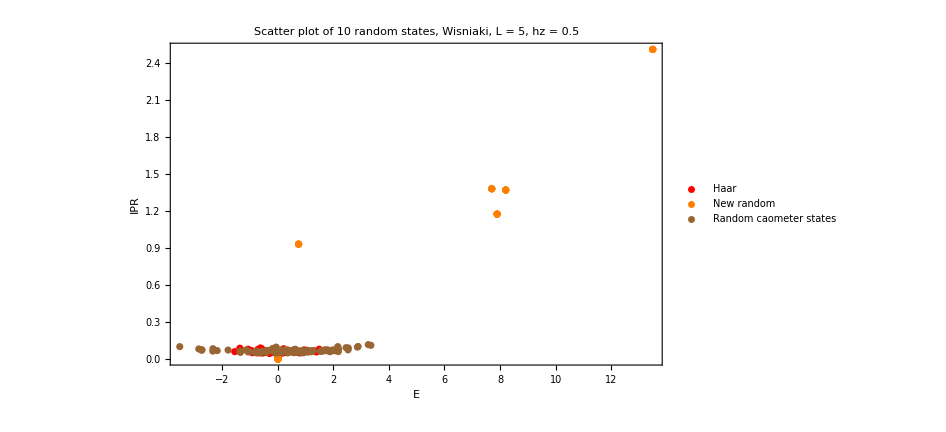

```mathematica
ListPlot[{Transpose[{energiesa,iprsa}],Transpose[{energiesb,iprsb}],Transpose[{energiesc,iprsc}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random caometer states",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],HoldForm[TraditionalForm[IPR]]}]
```

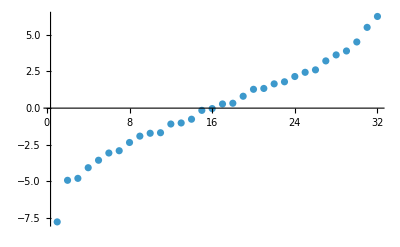

```mathematica
ListPlot[eigenval,PlotRange->All]
```

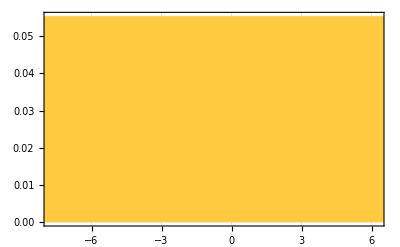

```mathematica
(*Define energy range and bin width*){emin,emax}={Min[eigenval],Max[eigenval]};
binWidth=20*Mean[Differences[Sort[eigenval+Min[eigenval]]]];
(*Create histogram bins for density of states*)
DOS=Histogram[eigenval,{binWidth},"ProbabilityDensity",PlotRange->{{emin,emax},All},PlotTheme->"Detailed",PlotRange->All]
```

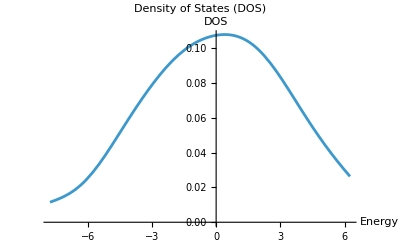

```mathematica
(*Kernel Density Estimate for smoother DOS*)dosDensity=SmoothKernelDistribution[eigenval];
(*Plot the smoothed density of states*)
Plot[PDF[dosDensity,e],{e,emin,emax},PlotLabel->"Density of States (DOS)",AxesLabel->{"Energy","DOS"}]
```

```mathematica
ipreigen=ParallelTable[Total[Abs[i]^4],{i,eigenvec}];
```

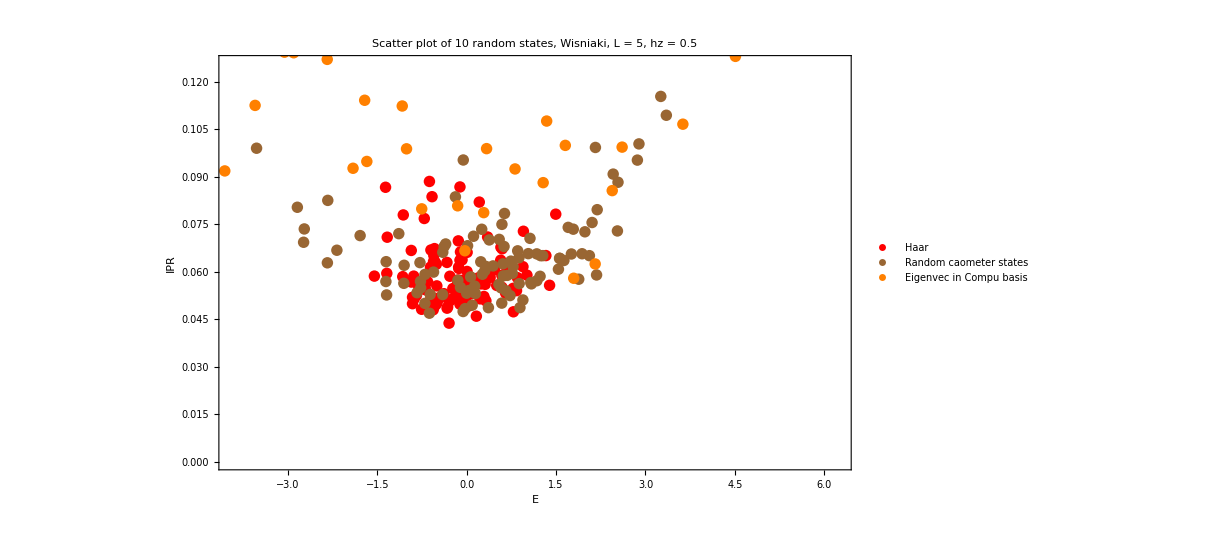

```mathematica
ListPlot[{Transpose[{energiesa,iprsa}],Transpose[{energiesc,iprsc}],Transpose[{eigenval,ipreigen}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Brown,Orange},PlotLegends->{Style["Haar",Red],Style["Random caometer states",Brown],Style["Eigenvec in Compu basis",Orange]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],HoldForm[TraditionalForm[IPR]]},ImageSize->900]
```

```mathematica
iprsa=ParallelTable[Total[Abs[i]^4],{i,ψa}];
iprsc=ParallelTable[Total[Abs[i]^4],{i,ψc}];
```

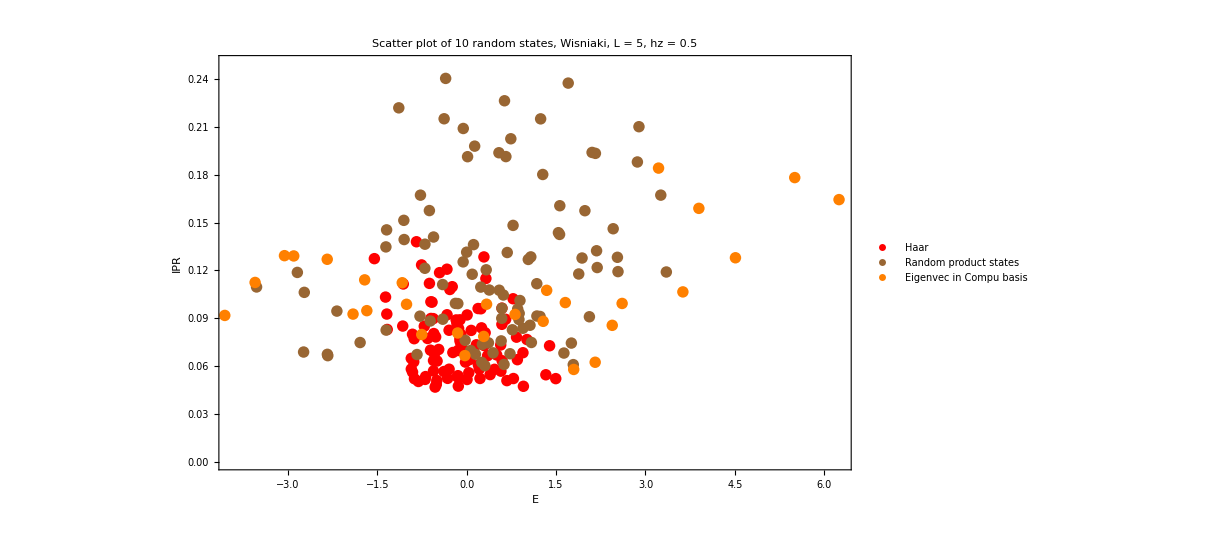

```mathematica
ListPlot[{Transpose[{energiesa,iprsa}],Transpose[{energiesc,iprsc}],Transpose[{eigenval,ipreigen}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Brown,Orange},PlotLegends->{Style["Haar",Red],Style["Random product states",Brown],Style["Eigenvec in Compu basis",Orange]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],HoldForm[TraditionalForm[IPR]]},ImageSize->900]
```

```mathematica
ale=10;
caometer=Table[haar[1],{i,ale}];
ψTa=Table[haar[L-1],{i,ale}];
ψTc=Table[RandomChainProductState[L-1],{i,ale}];
```

```mathematica
ψa=ArrayReshape[ParallelTable[Flatten[KroneckerProduct[i,j]],{j,ψTa},{i,caometer}],{ale*ale,2^L}];
ψc=ArrayReshape[ParallelTable[Flatten[KroneckerProduct[i,j]],{j,ψTc},{i,caometer}],{ale*ale,2^L}];
```

```mathematica
energiesa=ParallelTable[Chop[Conjugate[i].H.i],{i,ψa}];
energiesc=ParallelTable[Chop[Conjugate[i].H.i],{i,ψc}];
```

```mathematica
ListPlot[eigenval,PlotRange->All]
```

-Graphics-

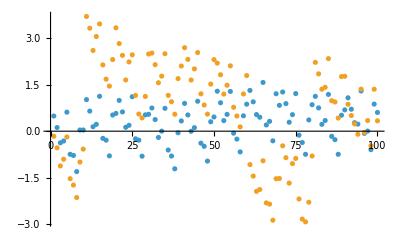

```mathematica
ListPlot[{energiesa,energiesc},PlotRange->All]
```

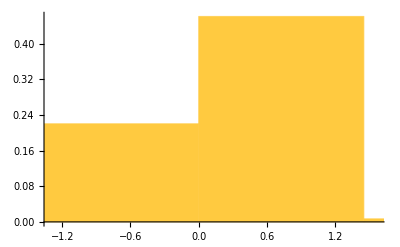

```mathematica
(*Define energy range and bin width*){emin,emax}={Min[energiesa],Max[energiesa]};
binWidth=50*Mean[Differences[Sort[energiesa+Min[energiesa]]]];
(*Create histogram bins for density of states*)
dosHistograma=Histogram[energiesa,{binWidth},"ProbabilityDensity",PlotRange->{{emin,emax},All}]
```

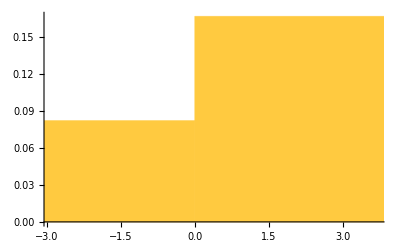

```mathematica
(*Define energy range and bin width*){emin,emax}={Min[energiesc],Max[energiesc]};
binWidth=60*Mean[Differences[Sort[energiesc+Min[energiesc]]]];
(*Create histogram bins for density of states*)
dosHistogramc=Histogram[energiesc,{binWidth},"ProbabilityDensity",PlotRange->{{emin,emax},All}]
```

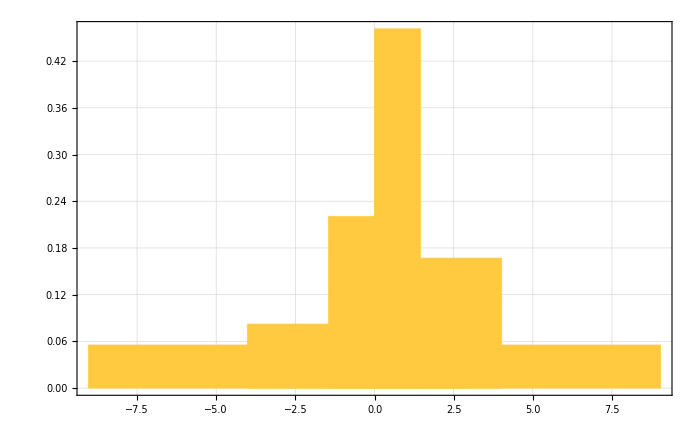

```mathematica
Show[{DOS, dosHistograma, dosHistogramc},PlotRange->All,ImageSize->700]
```

```mathematica
(*Find positions of elements within the range-2 to 2*)
positionsa=Position[energiesa,x_/;-3<=x<=3];
positionsc=Position[energiesc,x_/;-3<=x<=3];
```

```mathematica
eigenψa=Table[Conjugate[eigenvec].ψa[[i]],{i,Flatten[positionsa]}];
eigenψc=Table[Conjugate[eigenvec].ψc[[i]],{i,Flatten[positionsc]}];
```

```mathematica
iprsa=ParallelTable[Total[Abs[i]^4],{i,eigenψa}];
iprsc=ParallelTable[Total[Abs[i]^4],{i,eigenψc}];
```

## Magnetization and SP(t)

```mathematica
ope=Jz[L];
maga=Table[Chop[Conjugate[i].ope.i],{i,ψa}];
magb=Table[Chop[Conjugate[i].ope.i],{i,ψb}];
magc=Table[Chop[Conjugate[i].ope.i],{i,ψc}];
ope2=Jz[L].Jz[L];
maga=Table[Chop[Conjugate[i].ope.i],{i,ψa}];
magb=Table[Chop[Conjugate[i].ope.i],{i,ψb}];
magc=Table[Chop[Conjugate[i].ope.i],{i,ψc}];
vara=Table[Chop[Conjugate[ψa[[i]]].ope2.ψa[[i]]]-maga[[i]],{i,Length[ψa]}];
varb=Table[Chop[Conjugate[ψb[[i]]].ope2.ψb[[i]]]-magb[[i]],{i,Length[ψb]}];
varc=Table[Chop[Conjugate[ψc[[i]]].ope2.ψc[[i]]]-magc[[i]],{i,Length[ψc]}];
```

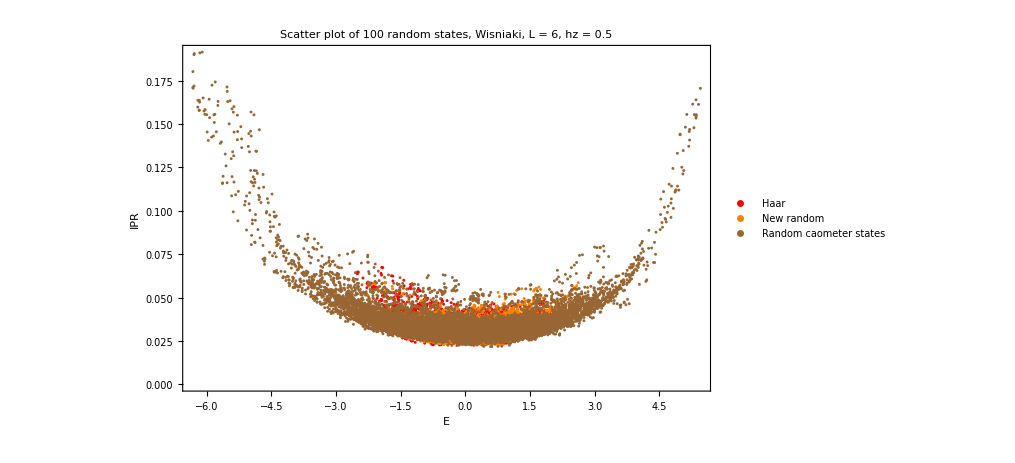

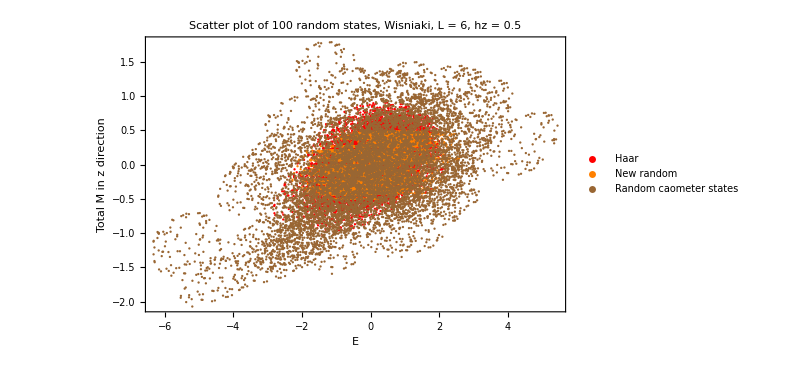

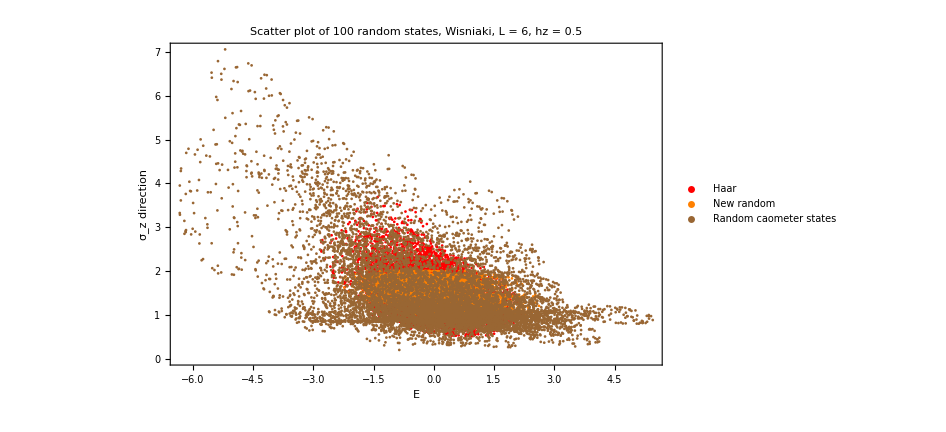

```mathematica
ListPlot[{Transpose[{energiesa,maga}],Transpose[{energiesb,magb}],Transpose[{energiesc,magc}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random caometer states",Brown]},FrameStyle->Directive[Black,FontSize->28],FrameLabel->{Style["E"],Style["Total M in z direction"]}]
ListPlot[{Transpose[{energiesa,vara}],Transpose[{energiesb,varb}],Transpose[{energiesc,varc}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random caometer states",Brown]},FrameStyle->Directive[Black,FontSize->28],FrameLabel->{Style["E"],Style["σ_z direction"]}]
```

```mathematica
ψat=Table[StateEvolution[t,ψa[[1]],eigenval,eigenvec],{t,0,50,0.1}];
ψbt=Table[StateEvolution[t,ψb[[1]],eigenval,eigenvec],{t,0,50,0.1}];
ψct=Table[StateEvolution[t,ψc[[1]],eigenval,eigenvec],{t,0,50,0.1}];
```

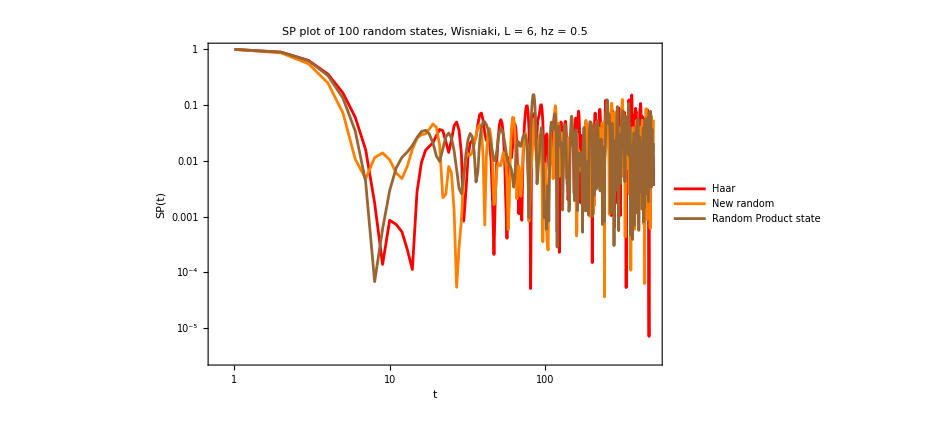

```mathematica
ListLogLogPlot[{Table[Abs[Conjugate[ψa[[1]]].i]^2,{i,ψat}],Table[Abs[Conjugate[ψb[[1]]].i]^2,{i,ψbt}],Table[Abs[Conjugate[ψc[[1]]].i]^2,{i,ψct}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["SP plot of "<>ToString[ale]<>" random states, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["SP(t)"]}]
```

```mathematica
densitya=Table[Dyad[i,i],{i,ψat}];
densityb=Table[Dyad[i,i],{i,ψbt}];
densityc=Table[Dyad[i,i],{i,ψct}];
```

```mathematica
reduceda=Table[Chop[MatrixPartialTrace[i,2,{2,2^(L-1)}]],{i,densitya}];
reducedb=Table[Chop[MatrixPartialTrace[i,2,{2,2^(L-1)}]],{i,densityb}];
reducedc=Table[Chop[MatrixPartialTrace[i,2,{2,2^(L-1)}]],{i,densityc}];
```

```mathematica
puritiesa=ParallelTable[Chop[Purity[i]],{i,reduceda}];
puritiesb=ParallelTable[Chop[Purity[i]],{i,reducedb}];
puritiesc=ParallelTable[Chop[Purity[i]],{i,reducedc}];
```

```mathematica
tlist=Range[0,50,0.1];
```

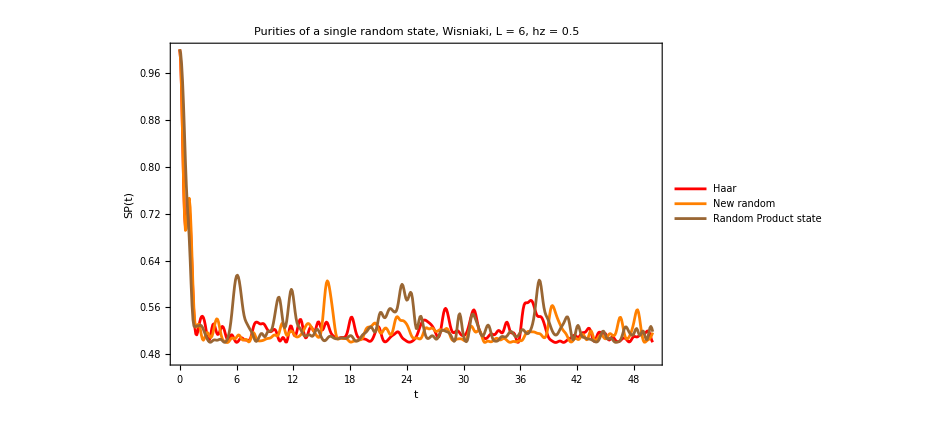

```mathematica
ListPlot[{Transpose[{tlist,puritiesa}],Transpose[{tlist,puritiesb}],Transpose[{tlist,puritiesc}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Purities of a single random state, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Orange,Brown},ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["SP(t)"]},PlotRange->All]
```

```mathematica
reducedmagax=Table[Chop[Tr[sx.i]],{i,reduceda}];
reducedmagay=Table[Chop[Tr[sy.i]],{i,reduceda}];
reducedmagaz=Table[Chop[Tr[sz.i]],{i,reduceda}];
reducedmagbx=Table[Chop[Tr[sx.i]],{i,reducedb}];
reducedmagby=Table[Chop[Tr[sy.i]],{i,reducedb}];
reducedmagbz=Table[Chop[Tr[sz.i]],{i,reducedb}];
reducedmagcx=Table[Chop[Tr[sx.i]],{i,reducedc}];
reducedmagcy=Table[Chop[Tr[sy.i]],{i,reducedc}];
reducedmagcz=Table[Chop[Tr[sz.i]],{i,reducedc}];
```

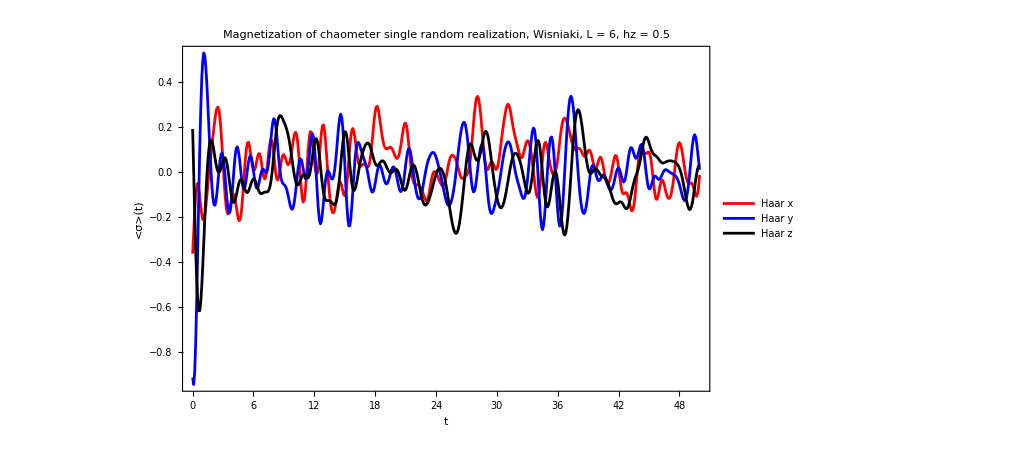

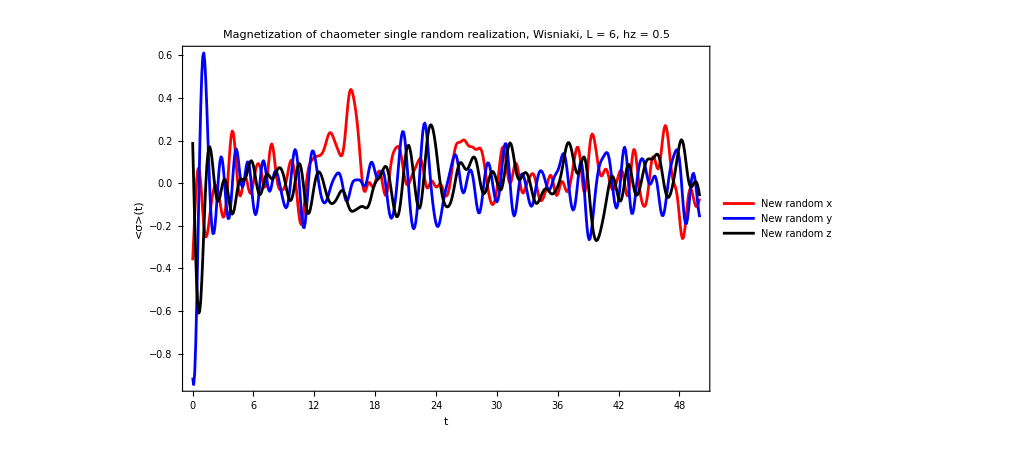

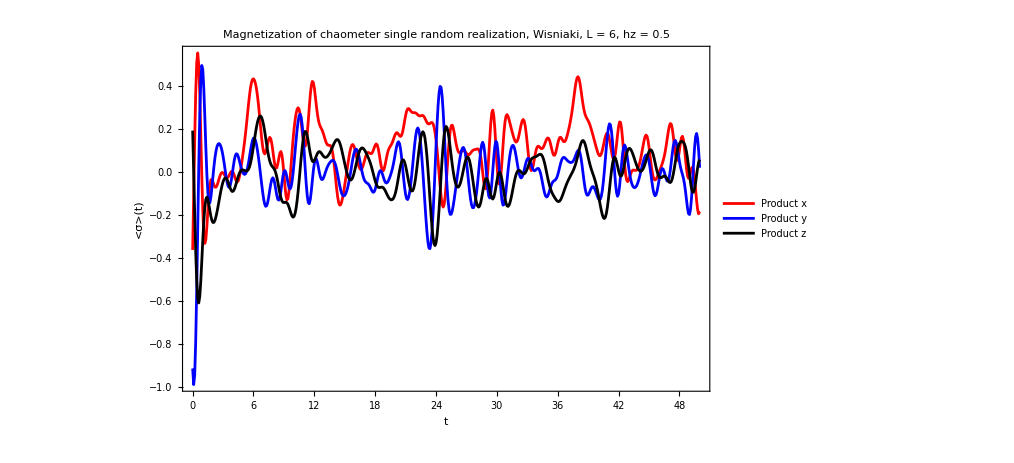

```mathematica
ListPlot[{Transpose[{tlist,reducedmagax}],Transpose[{tlist,reducedmagay}],Transpose[{tlist,reducedmagaz}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Magnetization of chaometer single random realization, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Directive[Red],Directive[Blue],Directive[Black]},ImageSize->750,PlotLegends->{Style["Haar x",Red],Style["Haar y",Blue],Style["Haar z",Black]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["<σ>(t)"]},PlotRange->All]

ListPlot[{Transpose[{tlist,reducedmagbx}],Transpose[{tlist,reducedmagby}],Transpose[{tlist,reducedmagbz}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Magnetization of chaometer single random realization, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Directive[Red],Directive[Blue],Directive[Black]},ImageSize->750,PlotLegends->{Style["New random x",Red],Style["New random y",Blue],Style["New random z",Black]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["<σ>(t)"]},PlotRange->All]

ListPlot[{Transpose[{tlist,reducedmagcx}],Transpose[{tlist,reducedmagcy}],Transpose[{tlist,reducedmagcz}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Magnetization of chaometer single random realization, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Directive[Red],Directive[Blue],Directive[Black]},ImageSize->750,PlotLegends->{Style["Product x",Red],Style["Product y",Blue],Style["Product z",Black]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["<σ>(t)"]},PlotRange->All]
```

```mathematica
testplot=-Graphics-
```

-Graphics-

```mathematica
Export["randomstates_sizeL.png",testplot,ImageSize->1000,ImageResolution->300]
```

randomstates_sizeL.png

## Regular

```mathematica
L=5;
hx=J=1.;
hz=4.0;
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

```mathematica
caometer=Table[haar[1],{i,50}];
```

```mathematica
ψa=Table[Flatten[KroneckerProduct[i,haar[L-1]]],{i,caometer}];
ψb=Table[Flatten[KroneckerProduct[i,Normalize[Table[Exp[i*I*RandomReal[]],{i,2^(L-1)}]]]],{i,caometer}];
ψc=Table[Flatten[KroneckerProduct[i,RandomChainProductState[L-1]]],{i,caometer}];
```

```mathematica
eigenψa=ParallelTable[Conjugate[eigenvec].i,{i,ψa}];
eigenψb=ParallelTable[Conjugate[eigenvec].i,{i,ψb}];
eigenψc=ParallelTable[Conjugate[eigenvec].i,{i,ψc}];
```

```mathematica
iprsa=ParallelTable[Total[Abs[i]^4],{i,eigenψa}];
iprsb=ParallelTable[Total[Abs[i]^4],{i,eigenψb}];
iprsc=ParallelTable[Total[Abs[i]^4],{i,eigenψc}];
```

```mathematica
energiesa=Table[Chop[Conjugate[i].H.i],{i,ψa}];
energiesb=Table[Chop[Conjugate[i].H.i],{i,ψb}];
energiesc=Table[Chop[Conjugate[i].H.i],{i,ψc}];
```

```mathematica
ope=Jz[L];
```

```mathematica
maga=Table[Chop[Conjugate[i].ope.i],{i,ψa}];
magb=Table[Chop[Conjugate[i].ope.i],{i,ψb}];
magc=Table[Chop[Conjugate[i].ope.i],{i,ψc}];
```

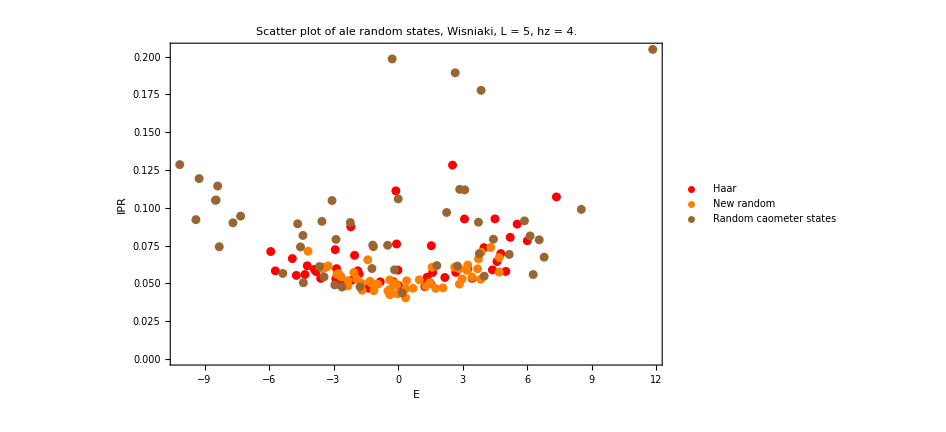

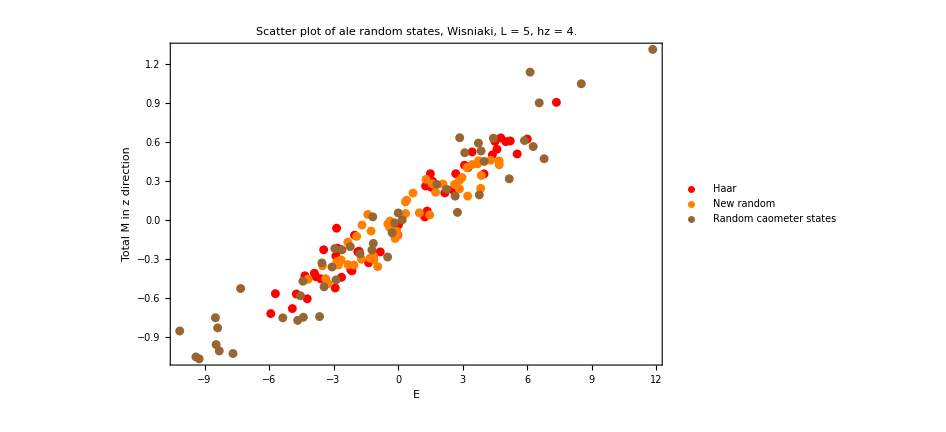

```mathematica
ListPlot[{Transpose[{energiesa,iprsa}],Transpose[{energiesb,iprsb}],Transpose[{energiesc,iprsc}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random caometer states",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],HoldForm[TraditionalForm[IPR]]}]
ListPlot[{Transpose[{energiesa,maga}],Transpose[{energiesb,magb}],Transpose[{energiesc,magc}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random caometer states",Brown]},FrameStyle->Directive[Black,FontSize->28],FrameLabel->{Style["E"],Style["Total M in z direction"]}]
```

```mathematica
ψat=Table[StateEvolution[t,ψa[[1]],eigenval,eigenvec],{t,0,50,0.1}];
ψbt=Table[StateEvolution[t,ψb[[1]],eigenval,eigenvec],{t,0,50,0.1}];
ψct=Table[StateEvolution[t,ψc[[1]],eigenval,eigenvec],{t,0,50,0.1}];
```

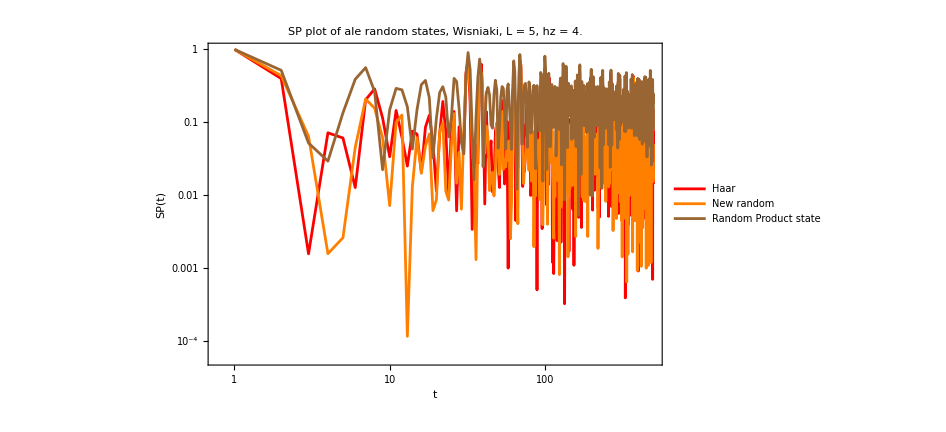

```mathematica
ListLogLogPlot[{Table[Abs[Conjugate[ψa[[1]]].i]^2,{i,ψat}],Table[Abs[Conjugate[ψb[[1]]].i]^2,{i,ψbt}],Table[Abs[Conjugate[ψc[[1]]].i]^2,{i,ψct}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["SP plot of "<>ToString[ale]<>" random states, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["SP(t)"]}]
```

```mathematica
densitya=ParallelTable[Dyad[i,i],{i,ψat}];
densityb=ParallelTable[Dyad[i,i],{i,ψbt}];
densityc=ParallelTable[Dyad[i,i],{i,ψct}];
```

```mathematica
reduceda=ParallelTable[Chop[MatrixPartialTrace[i,2,{2,2^(L-1)}]],{i,densitya}];
reducedb=ParallelTable[Chop[MatrixPartialTrace[i,2,{2,2^(L-1)}]],{i,densityb}];
reducedc=ParallelTable[Chop[MatrixPartialTrace[i,2,{2,2^(L-1)}]],{i,densityc}];
```

```mathematica
puritiesa=ParallelTable[Chop[Purity[i]],{i,reduceda}];
puritiesb=ParallelTable[Chop[Purity[i]],{i,reducedb}];
puritiesc=ParallelTable[Chop[Purity[i]],{i,reducedc}];
```

```mathematica
tlist=Range[0,50,0.1];
```

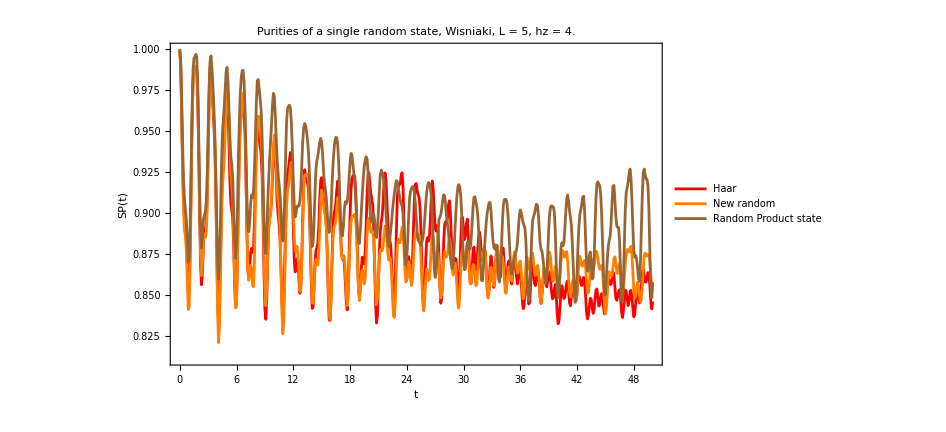

```mathematica
ListPlot[{Transpose[{tlist,puritiesa}],Transpose[{tlist,puritiesb}],Transpose[{tlist,puritiesc}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Purities of a single random state, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Orange,Brown},ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["SP(t)"]},PlotRange->All]
```

```mathematica
reducedmagax=Table[Chop[Tr[sx.i]],{i,reduceda}];
reducedmagay=Table[Chop[Tr[sy.i]],{i,reduceda}];
reducedmagaz=Table[Chop[Tr[sz.i]],{i,reduceda}];
reducedmagbx=Table[Chop[Tr[sx.i]],{i,reducedb}];
reducedmagby=Table[Chop[Tr[sy.i]],{i,reducedb}];
reducedmagbz=Table[Chop[Tr[sz.i]],{i,reducedb}];
reducedmagcx=Table[Chop[Tr[sx.i]],{i,reducedc}];
reducedmagcy=Table[Chop[Tr[sy.i]],{i,reducedc}];
reducedmagcz=Table[Chop[Tr[sz.i]],{i,reducedc}];
```

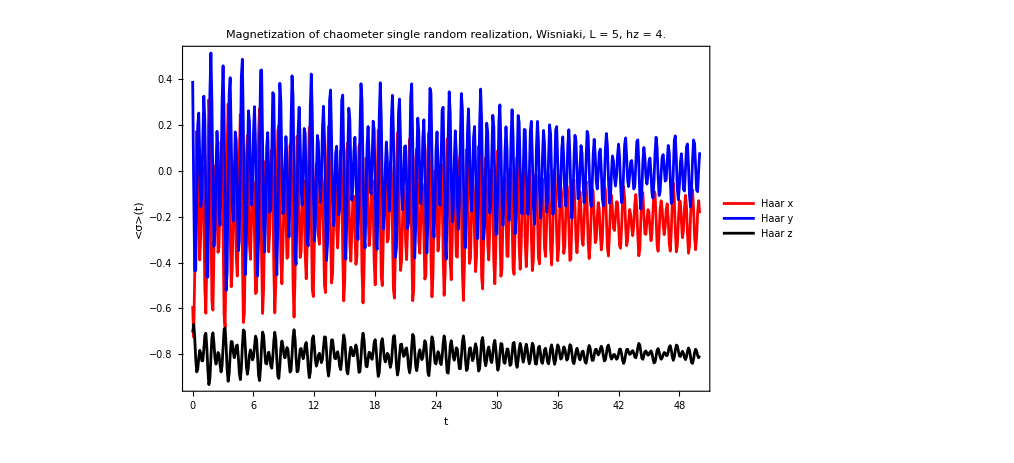

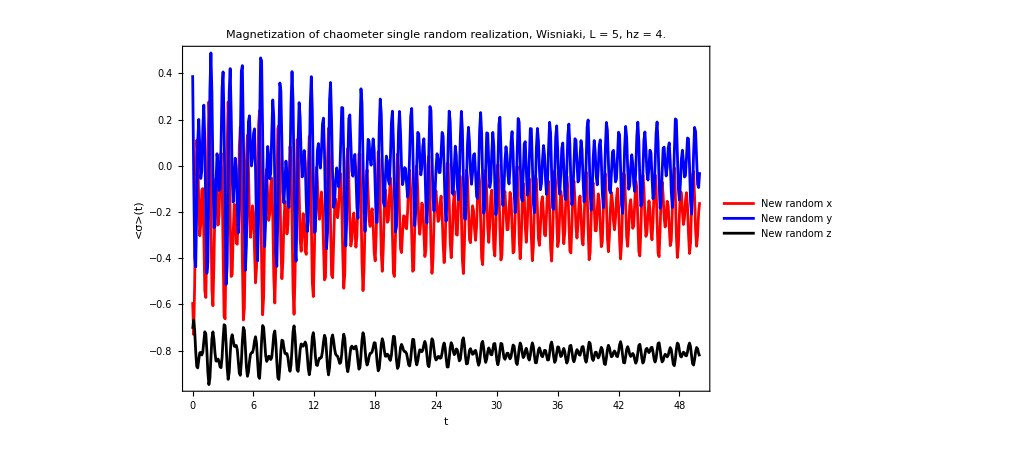

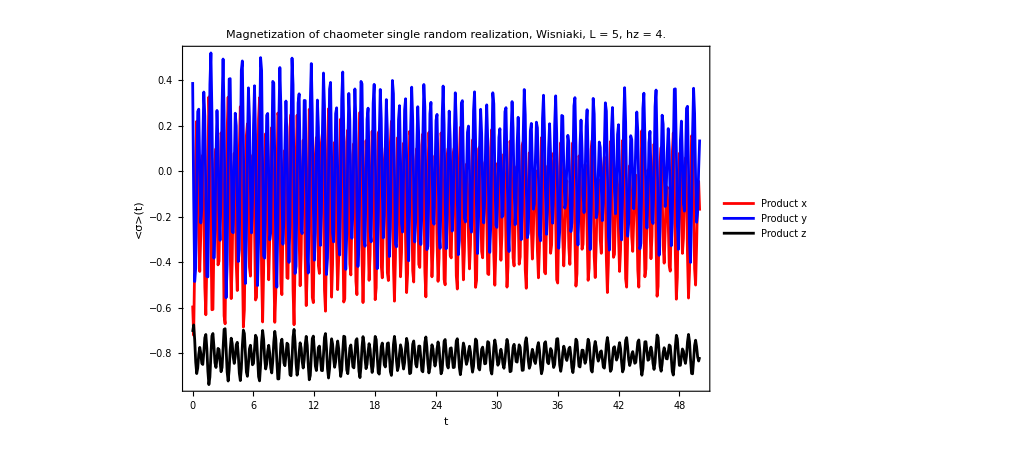

```mathematica
ListPlot[{Transpose[{tlist,reducedmagax}],Transpose[{tlist,reducedmagay}],Transpose[{tlist,reducedmagaz}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Magnetization of chaometer single random realization, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Directive[Red],Directive[Blue],Directive[Black]},ImageSize->750,PlotLegends->{Style["Haar x",Red],Style["Haar y",Blue],Style["Haar z",Black]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["<σ>(t)"]},PlotRange->All]

ListPlot[{Transpose[{tlist,reducedmagbx}],Transpose[{tlist,reducedmagby}],Transpose[{tlist,reducedmagbz}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Magnetization of chaometer single random realization, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Directive[Red],Directive[Blue],Directive[Black]},ImageSize->750,PlotLegends->{Style["New random x",Red],Style["New random y",Blue],Style["New random z",Black]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["<σ>(t)"]},PlotRange->All]

ListPlot[{Transpose[{tlist,reducedmagcx}],Transpose[{tlist,reducedmagcy}],Transpose[{tlist,reducedmagcz}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Magnetization of chaometer single random realization, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Directive[Red],Directive[Blue],Directive[Black]},ImageSize->750,PlotLegends->{Style["Product x",Red],Style["Product y",Blue],Style["Product z",Black]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["<σ>(t)"]},PlotRange->All]
```

## Random product states

```mathematica
L=9;
hx=J=1.;
hz=0.5;
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

```mathematica
ale=1000;
ψa=Table[haar[L],{i,ale}];
ψc=Table[RandomChainProductState[L],{i,ale}];
```

```mathematica
eigenψa=ParallelTable[Conjugate[eigenvec].i,{i,ψa}];
eigenψc=ParallelTable[Conjugate[eigenvec].i,{i,ψc}];
iprsa=ParallelTable[Total[Abs[i]^4],{i,eigenψa}];
iprsc=ParallelTable[Total[Abs[i]^4],{i,eigenψc}];
energiesa=Table[Chop[Conjugate[i].H.i],{i,ψa}];
energiesc=Table[Chop[Conjugate[i].H.i],{i,ψc}];
```

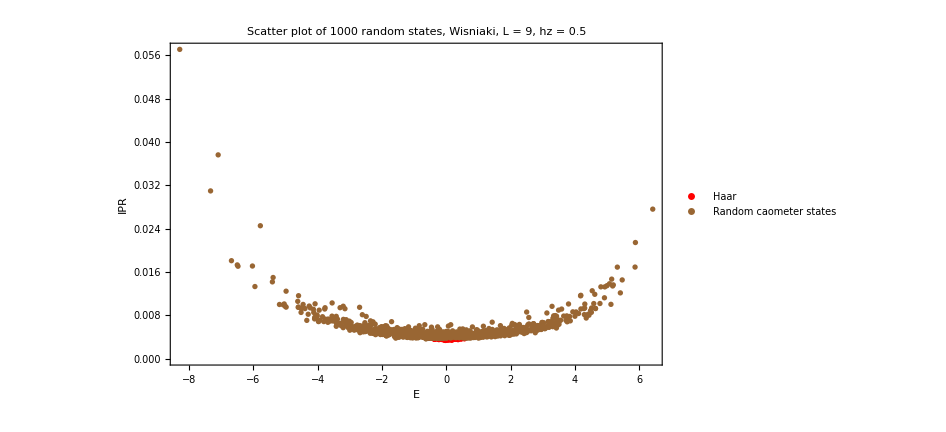

```mathematica
ListPlot[{Transpose[{energiesa,iprsa}],Transpose[{energiesc,iprsc}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["Random caometer states",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],HoldForm[TraditionalForm[IPR]]}]
```

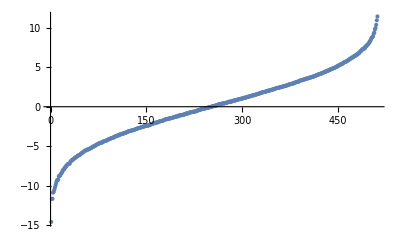

```mathematica
ListPlot[eigenval,PlotRange->All]
```

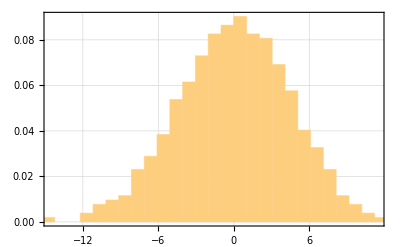

```mathematica
(*Define energy range and bin width*){emin,emax}={Min[eigenval],Max[eigenval]};
binWidth=20*Mean[Differences[Sort[eigenval+Min[eigenval]]]];
(*Create histogram bins for density of states*)
DOS=Histogram[eigenval,{binWidth},"ProbabilityDensity",PlotRange->{{emin,emax},All},PlotTheme->"Detailed",PlotRange->All]
```

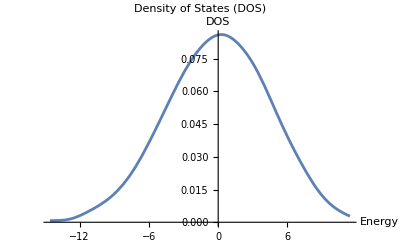

```mathematica
(*Kernel Density Estimate for smoother DOS*)dosDensity=SmoothKernelDistribution[eigenval];
(*Plot the smoothed density of states*)
Plot[PDF[dosDensity,e],{e,emin,emax},PlotLabel->"Density of States (DOS)",AxesLabel->{"Energy","DOS"}]
```

```mathematica
ipreigen=ParallelTable[Total[Abs[i]^4],{i,eigenvec}];
```

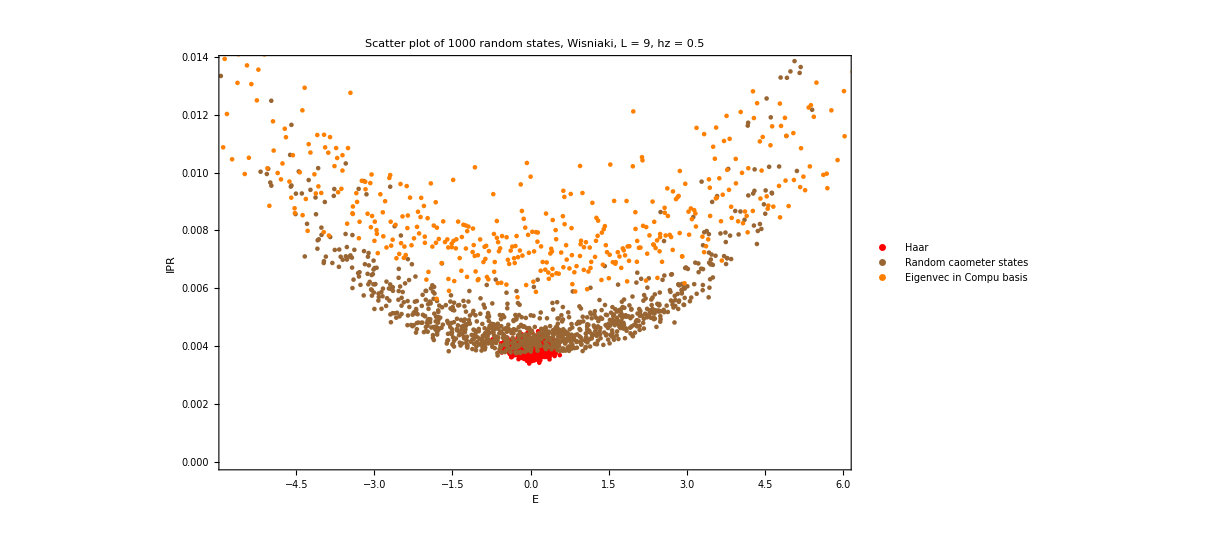

```mathematica
ListPlot[{Transpose[{energiesa,iprsa}],Transpose[{energiesc,iprsc}],Transpose[{eigenval,ipreigen}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Brown,Orange},PlotLegends->{Style["Haar",Red],Style["Random caometer states",Brown],Style["Eigenvec in Compu basis",Orange]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],HoldForm[TraditionalForm[IPR]]},ImageSize->900]
```

```mathematica
iprsa=ParallelTable[Total[Abs[i]^4],{i,ψa}];
iprsc=ParallelTable[Total[Abs[i]^4],{i,ψc}];
```

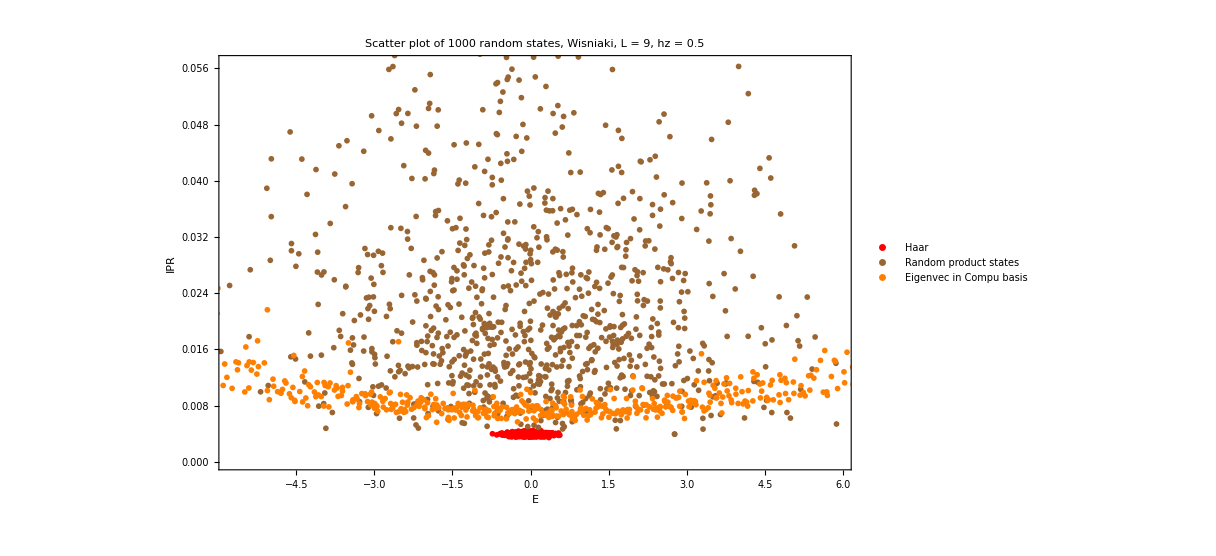

```mathematica
ListPlot[{Transpose[{energiesa,iprsa}],Transpose[{energiesc,iprsc}],Transpose[{eigenval,ipreigen}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Brown,Orange},PlotLegends->{Style["Haar",Red],Style["Random product states",Brown],Style["Eigenvec in Compu basis",Orange]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],HoldForm[TraditionalForm[IPR]]},ImageSize->900]
```

# Purities

```mathematica
L=5;
hx=1;
J=1;
hz=0.5;
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
ale2=30;
coloursc=Table[RGBColor[i,i/ale2,1-i],{i,ale2}];
blochtest=Table[qubit[i,0],{i,0,Pi,Pi/(ale2-1)}];
```

```mathematica
ψTa=qubit[0,0];
ψa=Table[Flatten[KroneckerProduct[ψTa,coherentstate[i,L-1]]],{i,blochtest}];
eigenψa=ParallelTable[Conjugate[eigenvec].i,{i,ψa}];
iprsa=ParallelTable[Total[Abs[i]^4],{i,eigenψa}];
energiesa=Table[Chop[Conjugate[i].H.i],{i,ψa}];
```

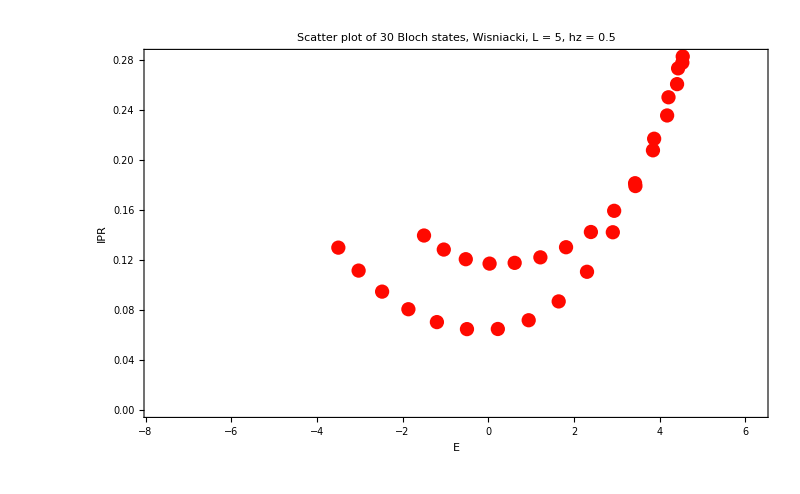

```mathematica
ListPlot[Transpose[{energiesa,iprsa}],PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale2]<>" Bloch states, Wisniacki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->coloursc[[1]],PlotRange->{{Min[eigenval],Max[eigenval]},All},ImageSize->800,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],HoldForm[TraditionalForm[IPR]]}]
```

```mathematica
tf=10.;
dt=0.1;
tlist=Range[0,tf,dt];
ψat=Table[StateEvolution[t,j,eigenval,eigenvec],{j,ψa},{t,0,tf,dt}];
```

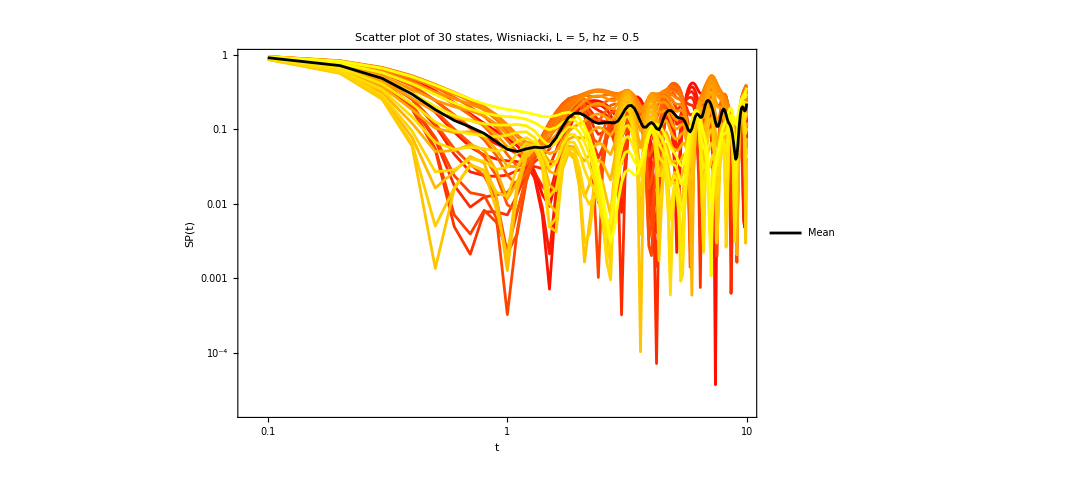

```mathematica
singlea=ListLogLogPlot[Table[{tlist[[i]],Abs[Conjugate[ψat[[j,1]]].ψat[[j,i]]]^2},{j,Length[ψat]},{i,Length[Range[0,tf,dt]]}],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale2]<>" states, Wisniacki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->coloursc,PlotRange->All,ImageSize->700,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["SP(t)"]}];
meana=ListLogLogPlot[Mean[Table[{tlist[[i]],Abs[Conjugate[ψat[[j,1]]].ψat[[j,i]]]^2},{j,Length[ψat]},{i,Length[Range[0,tf,dt]]}]],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale2]<>" states, Wisniacki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Directive[Black,Opacity[1]]},PlotRange->All,ImageSize->700,PlotLegends->{Style["Mean",Black]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["SP(t)"]}];
sp=Show[{singlea,meana},ImageSize->800]
```

```mathematica
ψat=Table[StateEvolution[t,j,eigenval,eigenvec],{j,ψa},{t,0,tf,dt}];
data={};
data2={};
Do[
densitya=Table[Dyad[j,j],{j,ψat[[k,All]]}];
reduceda=Table[Chop[MatrixPartialTrace[i,2,{2,2^(L-1)}]],{i,densitya}];
AppendTo[data2,reduceda];
puritiesa=Table[Chop[Purity[i]],{i,reduceda}];
AppendTo[data,puritiesa];
,{k,ale2}];
```

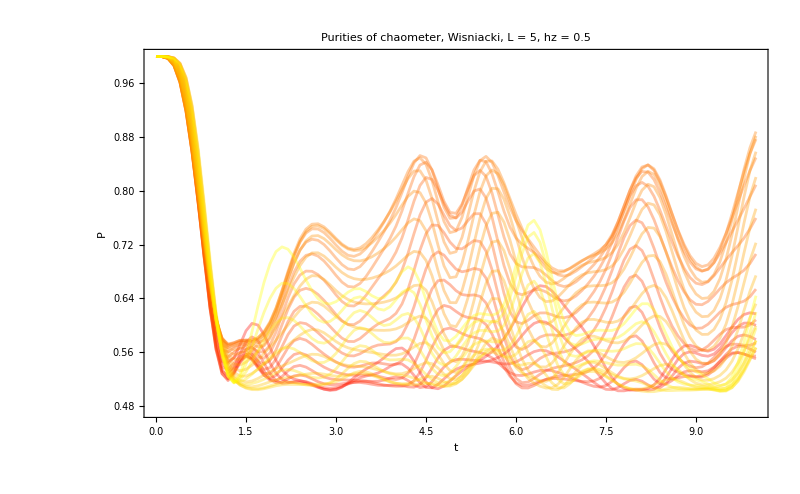

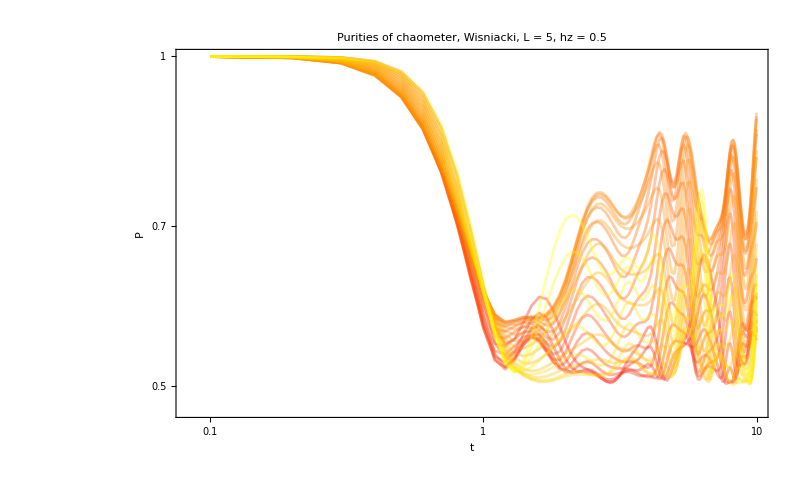

```mathematica
tlist=Range[0,tf,dt];
uno=ListPlot[Table[Transpose[{tlist,i}],{i,data}],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Purities of chaometer, Wisniacki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->Table[Directive[j,Opacity[0.35]],{j,coloursc}],PlotRange->All,ImageSize->800,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],HoldForm[P]}]
logpurity=ListLogLogPlot[Table[Transpose[{tlist,i}],{i,data}],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Purities of chaometer, Wisniacki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->Table[Directive[j,Opacity[0.35]],{j,coloursc}],PlotRange->All,ImageSize->800,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],HoldForm[P]}]
```

```mathematica
data2x={};
data2y={};
data2z={};
Do[
reducedmagax=Table[Chop[Tr[sx.i]],{i,data2[[k,All]]}];
reducedmagay=Table[Chop[Tr[sy.i]],{i,data2[[k,All]]}];
reducedmagaz=Table[Chop[Tr[sz.i]],{i,data2[[k,All]]}];
AppendTo[data2x,reducedmagax];
AppendTo[data2y,reducedmagay];
AppendTo[data2z,reducedmagaz];
,{k,ale2}];
```

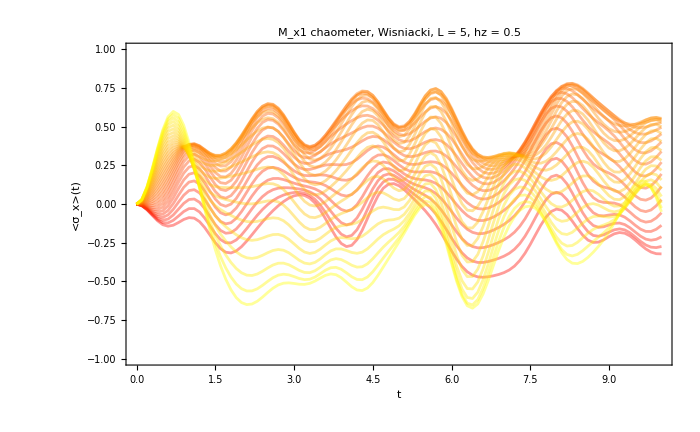

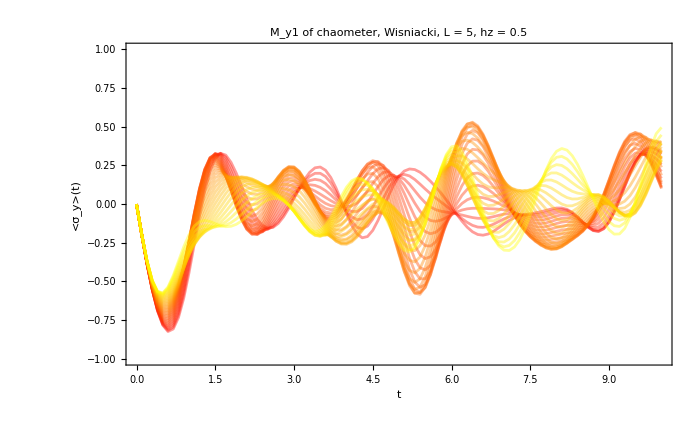

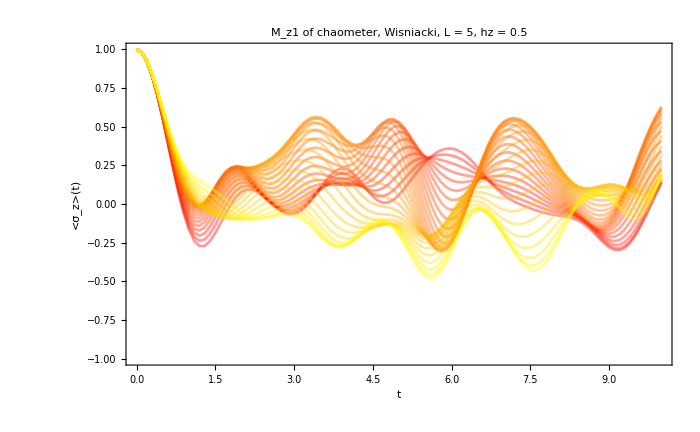

```mathematica
ListPlot[Table[Transpose[{tlist,k}],{k,data2x}],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["M_x1 chaometer, Wisniacki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->Table[Directive[j,Opacity[0.4]],{j,coloursc}],PlotRange->{All,{-1,1}},ImageSize->700,PlotLegends->Style["M_x(t)",Black,25],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["<σ_x>(t)"]}]
ListPlot[Table[Transpose[{tlist,k}],{k,data2y}],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["M_y1 of chaometer, Wisniacki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->Table[Directive[j,Opacity[0.4]],{j,coloursc}],PlotRange->{All,{-1,1}},ImageSize->700,PlotLegends->Style["M_y(t)",Black,25],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["<σ_y>(t)"]}]
ListPlot[Table[Transpose[{tlist,k}],{k,data2z}],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["M_z1 of chaometer, Wisniacki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->Table[Directive[j,Opacity[0.4]],{j,coloursc}],PlotRange->{All,{-1,1}},ImageSize->700,PlotLegends->Style["M_z(t)",Black,25],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["<σ_z>(t)"]}]
```

# Product states characterization Ising

```mathematica
L=8;
hx=1;
J=1;
hz=0.5;
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

```mathematica
ListPlot[Transpose[{eigenval,iprsc}],PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",35,Black],PlotStyle->{Directive[coloursc[[i]],Opacity[0.25]]},PlotRange->All,ImageSize->1000,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],HoldForm[TraditionalForm[IPR]]}]
```

```mathematica
ale=10;
caometer=Table[haar[1],{i,ale}];
ale2=10;
coloursc=Table[RGBColor[i,i/ale2,1-i],{i,ale2}];
single=qubit[0,0];
blochtest=Table[qubit[i,0],{i,0,Pi,Pi/(ale2-1)}];
```

# Choi matrix ising

```mathematica
J=1;
hx=1;
hz=3.0;
tlist=Table[10^i,{i,-2,16,0.0030}];
tlist//Length
```

6001

```mathematica
colors={Gray,Red,Blue,Brown,Purple};
texts={Style["RPS",25,Black],Style["Haar",25,Black],Style["Coherent state",25,Black],Style["{0,1} High PR",25,Black], Style["{0,1} Low PR",25,Black]};
La=1;
```

```mathematica
q=3;
Do[

Lb=L-La;
(*ψ=RandomChainProductState[Lb];*)
(*ψ=haar[Lb];*)
ψ=coherentstate[haar[1],Lb];
A=KroneckerProduct[IdentityMatrix[2^(Lb),SparseArray]/2^(La),Dyad[ψ]];
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenvals,eigenvecs}=Transpose[Sort[Transpose[Eigensystem[H]]]];
P=Transpose[eigenvecs];
Pinv=Conjugate[eigenvecs];
ClearAll[U];
U[t_]:=P.DiagonalMatrix[Exp[-I*eigenvals*t]].Pinv;
chois=ParallelTable[ChoiMatrix[U[t],A,La,Lb],{t,tlist},DistributedContexts->Full];
purity=ParallelTable[Chop[Tr[i.i]],{i,Chop[chois]},DistributedContexts->Full];
plot=ListLogLinearPlot[Transpose[{tlist,purity}],PlotTheme->"Detailed",PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", hz = "<>ToString[hz]<>", "<>ToString[texts[[q]]]<>" ψ_E",30,Black],Joined->True,Axes->True,GridLines->None,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Choi's Purity"]},PlotRange->All,ImageSize->1000,PlotStyle->{Directive[colors[[q]],Opacity[1.0]]},PlotLegends->{Style["ψ_E "<>ToString[texts[[q]]], colors[[q]],Opacity[1.0]]}];
final=Show[{plot,LogLinearPlot[0.25,{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Red,Dashed]],LogLinearPlot[0.5,{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Purple,Dashed]]}];
Export["choi_coherent_loglinear_purity_L_"<>ToString[L]<>"_La_"<>ToString[La]<>"_J_"<>ToString[J]<>"_hz_"<>ToString[hz]<>"_.png",final,ImageResolution->300];

,{L,4,10,2}];
```

## Random phases

```mathematica
neweigenvals=RandomReal[{-1,1},2^L];
A=KroneckerProduct[IdentityMatrix[2^(Lb),SparseArray]/2^(La),Dyad[ψ]];
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenvals,eigenvecs}=Transpose[Sort[Transpose[Eigensystem[H]]]];
P=Transpose[eigenvecs];
Pinv=Conjugate[eigenvecs];
ClearAll[U];
U[t_]:=P.DiagonalMatrix[Exp[-I*neweigenvals*t]].Pinv;
fakechois=ParallelTable[ChoiMatrix[U[t],A,La,Lb],{t,tlist},DistributedContexts->Full];
fakechoieigenvals=ParallelTable[Chop[Eigenvalues[i]],{i,fakechois},DistributedContexts->Full];
fakepurity=ParallelTable[Chop[Tr[i.i]],{i,Chop[fakechois]},DistributedContexts->Full];
```

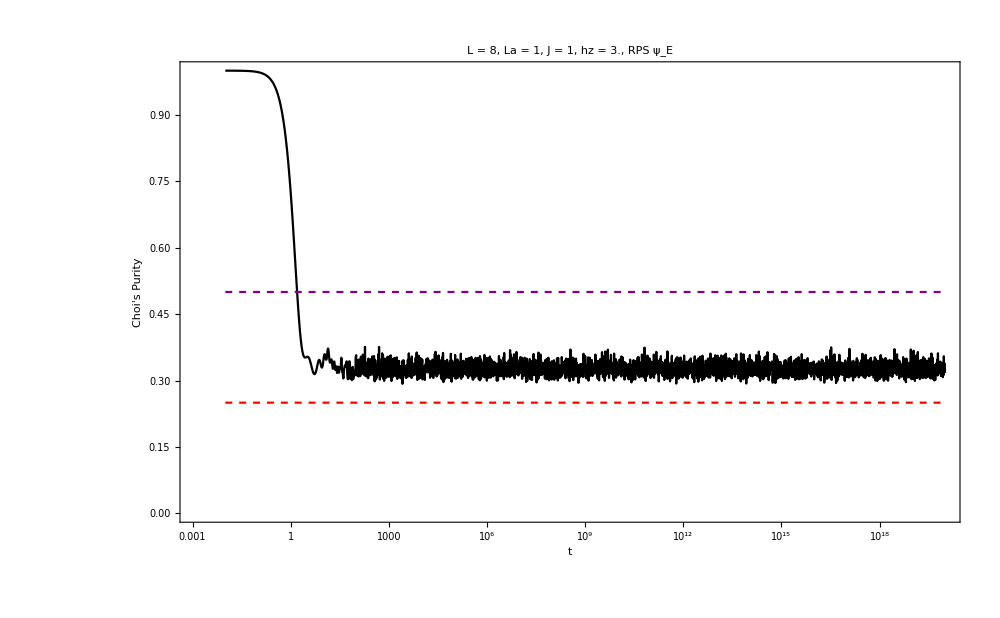

```mathematica
q=1;
plot2=ListLogLinearPlot[Transpose[{tlist,fakepurity}],PlotTheme->"Detailed",PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", hz = "<>ToString[hz]<>", "<>ToString[texts[[q]]]<>" ψ_E",30,Black],Joined->True,Axes->True,GridLines->None,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Choi's Purity"]},PlotRange->All,ImageSize->1000,PlotLegends->Automatic,PlotStyle->{Directive[Black,Opacity[1]]}];
final2=Show[{plot2,LogLinearPlot[0.25,{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Red,Dashed]],LogLinearPlot[0.5,{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Purple,Dashed]]}]
```

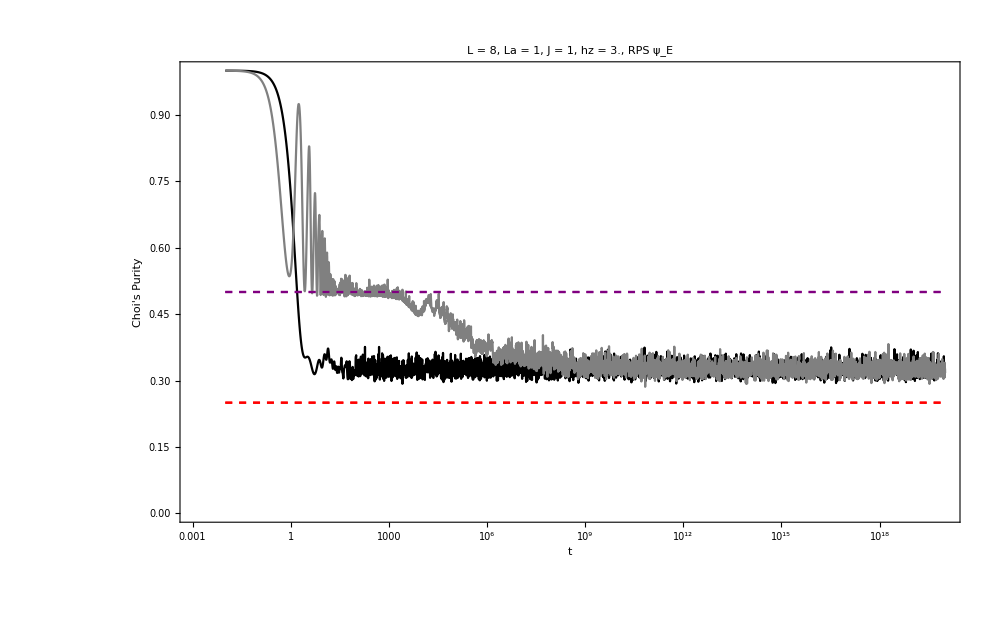

```mathematica
Show[{final2,final}]
```

## Coherent states on ψ_E

```mathematica
J=1;
hx=1;
hz=0.5;
tlist=Table[10^i,{i,-2,16,0.0030}];
tlist//Length
```

6001

```mathematica
colors={Gray,Red,Blue,Brown,Purple};
texts={Style["RPS",25,Black],Style["Haar",25,Black],Style["Coherent state",25,Black],Style["{0,1} High PR",25,Black]};
L=4;
La=1;
q=3;
Lb=L-La;
```

```mathematica
tone=Table[ColorData["DeepSeaColors"][i],{i,0.2,1,1/38}];
qubits=Table[qubit[θ,0],{θ,0,Pi,Pi/30}];
```

```mathematica
allplots={};
```

```mathematica
Do[

ψ=coherentstate[qubits[[i]],Lb];
A=KroneckerProduct[IdentityMatrix[2^(Lb),SparseArray]/2^(La),Dyad[ψ]];
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenvals,eigenvecs}=Transpose[Sort[Transpose[Eigensystem[H]]]];
P=Transpose[eigenvecs];
Pinv=Conjugate[eigenvecs];
ClearAll[U];
U[t_]:=P.DiagonalMatrix[Exp[-I*eigenvals*t]].Pinv;
chois=ParallelTable[ChoiMatrix[U[t],A,La,Lb],{t,tlist},DistributedContexts->Full];
purity=ParallelTable[Chop[Tr[i.i]],{i,Chop[chois]},DistributedContexts->Full];
plot=ListLogLinearPlot[Transpose[{tlist,purity}],PlotTheme->"Detailed",PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", hz = "<>ToString[hz]<>", "<>ToString[texts[[q]]]<>" ψ_E",30,Black],Joined->True,Axes->True,GridLines->None,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Choi's Purity"]},PlotRange->All,ImageSize->1000,PlotStyle->{Directive[tone[[i]],Opacity[1.0]]},PlotLegends->{Style["ψ_E "<>ToString[texts[[q]]], tone[[i]],Opacity[1.0]]}];
final=Show[{plot,LogLinearPlot[0.25,{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Red,Dashed]],LogLinearPlot[0.5,{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Purple,Dashed]]}];
Export["choi_coherent_"<>ToString[i]<>"_loglinear_purity_L_"<>ToString[L]<>"_La_"<>ToString[La]<>"_J_"<>ToString[J]<>"_hz_"<>ToString[hz]<>"_.png",final,ImageResolution->300];
AppendTo[allplots,final];

,{i,Length[qubits]}];
```

```mathematica
Export["choi_coherent_ALL_loglinear_purity_L_"<>ToString[L]<>"_La_"<>ToString[La]<>"_J_"<>ToString[J]<>"_hz_"<>ToString[hz]<>"_.gif",allplots,"DisplayDurations"->0.5,"AnimationRepetitions"->Infinity]
```

choi_coherent_ALL_loglinear_purity_L_4_La_1_J_1_hz_0.5_.gif

## High PR of {0,1}

```mathematica
L=8;
J=1;
hx=1;
hz=0.5;
tlist=Table[10^i,{i,-2,16,0.0030}];
tlist//Length
```

6001

```mathematica
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenvals,eigenvecs}=Transpose[Sort[Transpose[Eigensystem[H]]]];
```

```mathematica
productstate2=Table[IdentityMatrix[2^L][[i]],{i,2^L}];
```

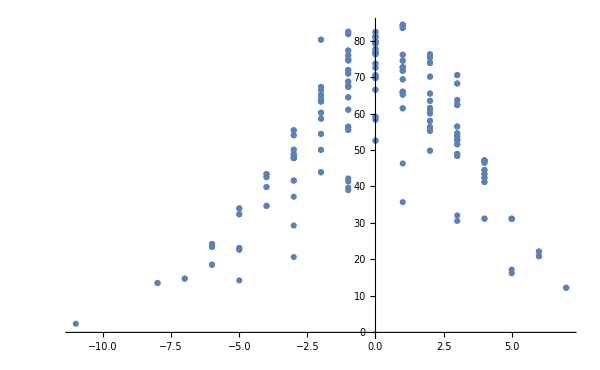

```mathematica
iprs=ParallelTable[Quiet[Total[Abs[Conjugate[eigenvecs].i]^4]],{i,productstate2},DistributedContexts->Full];
energies=ParallelTable[Chop[Conjugate[i].H.i],{i,productstate2},DistributedContexts->Full];
ListPlot[Transpose[{energies,1/iprs}],PlotRange->All,ImageSize->600]
```

```mathematica
Min[iprs]
```

0.0544625

```mathematica
threshold=0.06;
indexs=Flatten[Position[iprs,x_/;x<threshold]];
productstate=Table[productstate2[[i]],{i,indexs}];
productstate//Dimensions
```

{12,256}

```mathematica
Max[iprs]
```

0.421509

```mathematica
threshold=0.05;
indexs=Flatten[Position[iprs,x_/;x>threshold]];
productstate=Table[productstate2[[i]],{i,indexs}];
productstate//Dimensions
```

{12,256}

```mathematica
tone=Table[ColorData["ArmyColors"][i],{i,0.1,1,1/13}];
tone//Length
q=5;
```

12

```mathematica
allplots={};
```

```mathematica
Do[

Lb=L-La;
ψ=productstate[[i]];
rho=MatrixPartialTrace[Dyad[ψ],1,{2^La,2^Lb}];
A=KroneckerProduct[IdentityMatrix[2^(Lb),SparseArray]/2^(La),rho];
P=Transpose[eigenvecs];
Pinv=Conjugate[eigenvecs];
ClearAll[U];
U[t_]:=P.DiagonalMatrix[Exp[-I*eigenvals*t]].Pinv;
chois=ParallelTable[ChoiMatrix[U[t],A,La,Lb],{t,tlist},DistributedContexts->Full];
purity=ParallelTable[Chop[Tr[i.i]],{i,Chop[chois]},DistributedContexts->Full];
plot=ListLogLinearPlot[Transpose[{tlist,purity}],PlotTheme->"Detailed",PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", hz = "<>ToString[hz]<>", "<>ToString[texts[[q]]]<>" ψ_E",30,Black],Joined->True,Axes->True,GridLines->None,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Choi's Purity"]},PlotRange->All,ImageSize->1000,PlotStyle->{Directive[tone[[i]],Opacity[1.0]]},PlotLegends->{Style["ψ_E "<>ToString[texts[[q]]], tone[[i]],Opacity[1.0]]}];
final=Show[{plot,LogLinearPlot[0.25,{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Red,Dashed]],LogLinearPlot[0.5,{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Purple,Dashed]]}];
Export["choi_LOWPR_"<>ToString[i]<>"_loglinear_purity_L_"<>ToString[L]<>"_La_"<>ToString[La]<>"_J_"<>ToString[J]<>"_hz_"<>ToString[hz]<>"_.png",final,ImageResolution->300];
AppendTo[allplots,final];

,{i,Length[productstate]}];
```

```mathematica
Export["choi_LOWPR_ALL_loglinear_purity_L_"<>ToString[L]<>"_La_"<>ToString[La]<>"_J_"<>ToString[J]<>"_hz_"<>ToString[hz]<>"_.gif",allplots,"DisplayDurations"->0.5,"AnimationRepetitions"->Infinity]
```

choi_LOWPR_ALL_loglinear_purity_L_8_La_1_J_1_hz_0.5_.gif

# Choi matrix XXZ

```mathematica
L=8;
La=4;
Lb=L-La;
Δ=1;
```

```mathematica
ψ=haar[Lb];
```

```mathematica
ψ=coherentstate[haar[1],Lb];
```

```mathematica
x=RandomInteger[100000];
SeedRandom[x];
ψ=RandomChainProductState[Lb];
```

```mathematica
A=KroneckerProduct[IdentityMatrix[2^(Lb),SparseArray]/2^(Lb),Dyad[ψ]];
```

```mathematica
tlist=Table[10^i,{i,-1,6,0.01}];
tlist//Length
```

701

```mathematica
?OpenXXZHamiltonian
```

```mathematica
h1=h2=1;
Δ=1;
H=OpenXXZHamiltonian[L,Δ,h1,h2];
```

```mathematica
H=IsingNNOpenHamiltonian[1,0.5,1,L];
{eigenvals,eigenvecs}=Transpose[Sort[Transpose[Eigensystem[H]]]];
P=Transpose[eigenvecs];
Pinv=Conjugate[eigenvecs];
ClearAll[U];
U[t_]:=P.DiagonalMatrix[Exp[-I*eigenvals*t]].Pinv;
```

```mathematica
chois=ParallelTable[ChoiMatrix[U[t],A,La,Lb],{t,tlist},DistributedContexts->Full];
```

```mathematica
Table[Tr[i],{i,chois}]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

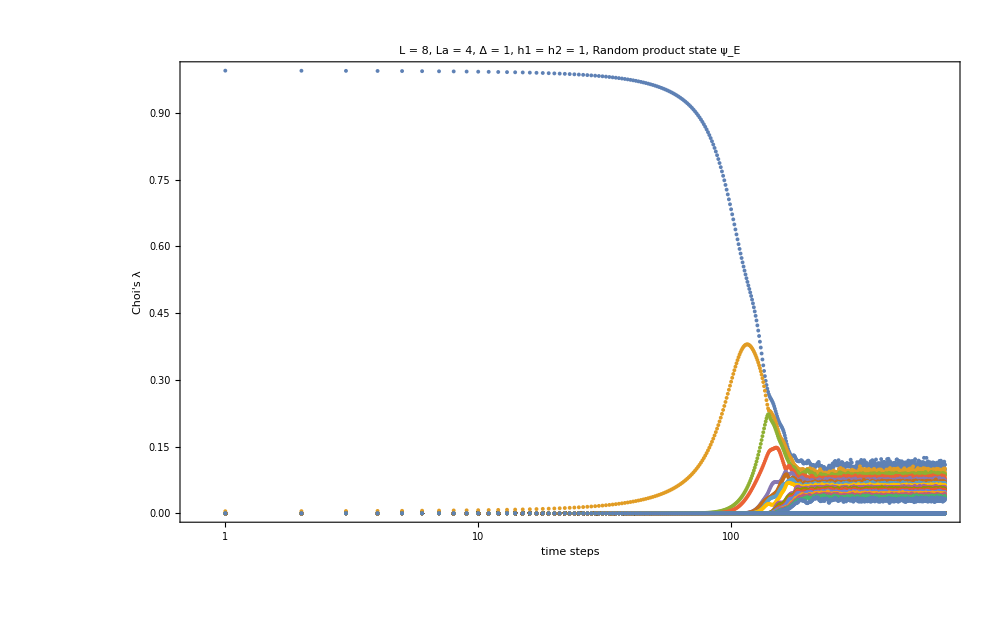

```mathematica
choieigenvals=ParallelTable[Chop[Eigenvalues[i]],{i,chois},DistributedContexts->Full];
svn=Table[Chop[Total[Map[VNentropy,i]]],{i,choieigenvals}];
plot=ListLogLinearPlot[Transpose[choieigenvals],PlotTheme->"Detailed",PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", Δ = "<>ToString[Δ]<>", h1 = h2 = "<>ToString[h1]<>", Random product state ψ_E",30,Black],Joined->False,Axes->True,GridLines->None,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["time steps"],Style["Choi's λ"]},PlotRange->All,ImageSize->1000]
(*Export["choi_eigenvals_L_"<>ToString[L]<>"_La_"<>ToString[La]<>"_J_"<>ToString[J]<>"_hz_"<>ToString[hz]<>"_.png",plot];*)
```

```mathematica
chois//Length
```

701

```mathematica
Sort[Chop[Eigenvalues[chois[[1]]]]]
Sort[Chop[Eigenvalues[chois[[100]]]]]
Sort[Chop[Eigenvalues[chois[[500]]]]]
Sort[Chop[Eigenvalues[chois[[-1]]]]]
```

{-7.9808×10^-10,-5.91975×10^-10,-4.79557×10^-10,-4.34968×10^-10,-3.90759×10^-10,-3.60931×10^-10,-2.23746×10^-10,-2.09774×10^-10,-1.86879×10^-10,-1.71665×10^-10,-1.41099×10^-10,-1.20646×10^-10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.20655×10^-10,1.41094×10^-10,1.71655×10^-10,1.86878×10^-10,2.09743×10^-10,2.23672×10^-10,3.60906×10^-10,3.90754×10^-10,4.34967×10^-10,4.79553×10^-10,5.91945×10^-10,7.98075×10^-10,1.10111×10^-9,0.0048092,0.995191}

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.89875×10^-10,4.49664×10^-10,1.57742×10^-7,3.91121×10^-7,6.7701×10^-6,0.0000173447,0.00599183,0.0145036,0.29593,0.68355}

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.0339488,0.0364297,0.0402511,0.0452062,0.0489929,0.0509477,0.054508,0.0562022,0.0586749,0.0644777,0.0708096,0.0727317,0.0797225,0.0879563,0.0968572,0.102284}

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0.0319542,0.0345201,0.0385596,0.0426254,0.0456972,0.0481529,0.0536956,0.0574104,0.0622837,0.0679472,0.0706161,0.071517,0.07708,0.0876362,0.100867,0.109437}

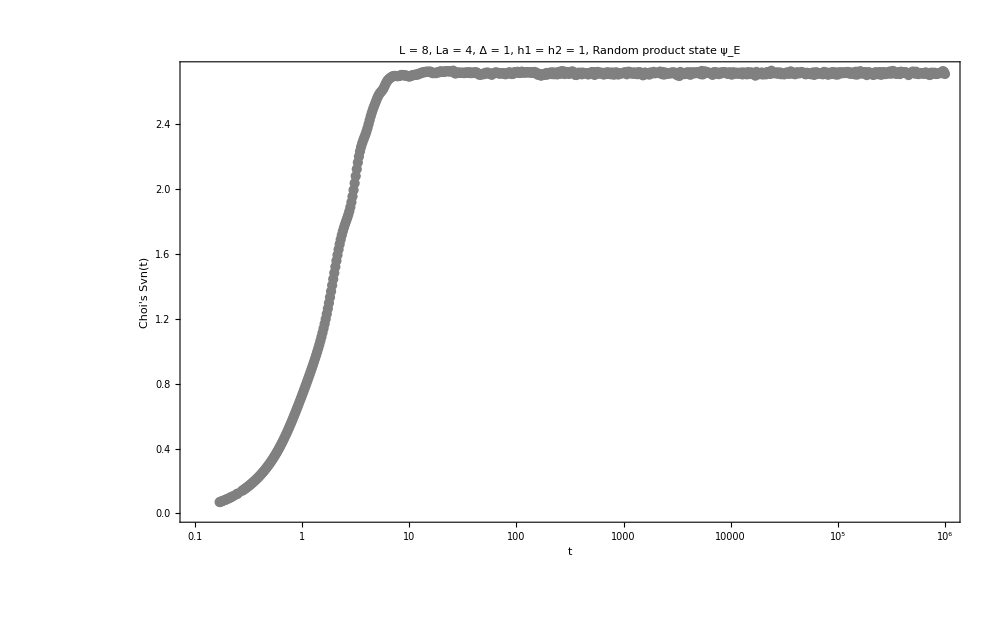

```mathematica
plot=ListLogLinearPlot[Transpose[{tlist,Chop[svn]}],PlotTheme->"Detailed",PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", Δ = "<>ToString[Δ]<>", h1 = h2 = "<>ToString[h1]<>", Random product state ψ_E",30,Black],Joined->False,Axes->True,GridLines->None,FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Choi's Svn(t)"]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},ImageSize->1000,PlotLegends->Automatic,PlotStyle->{Directive[Gray,Opacity[1.0]]}]
(*Export["choi_svn_L_"<>ToString[L]<>"_La_"<>ToString[La]<>"_J_"<>ToString[J]<>"_hz_"<>ToString[hz]<>"_.png",plot,ImageResolution->300];*)
```